```mathematica
n=225;
r=0.02;
v0 = 0.0001;
tx=Import["D:\\datax.txt","Table"];
ty=Import["D:\\datay.txt","Table"];
tx=Table[Table[tx[[i]],{i,j,j+n-1,1}],{j,1,Length[tx],n}];
ty=Table[Table[ty[[i]],{i,j,j+n-1,1}],{j,1,Length[ty],n}];
```

```mathematica
pict={};
Do[
temp=Table[{tx[[j,i]][[1]],ty[[j,i]][[1]]},{i,1,n}];
g1=Graphics[{Red,Disk[#,r]}]&/@temp;
g2=Graphics[{Black,Thick,Line[#]}]&/@{{{-0.5,-0.5},{-0.5,0.5}},{{0.5,-0.5},{0.5,0.5}},{{-0.5,0.5},{0.5,0.5}},{{-0.5,-0.5},{0.5,-0.5}}};
g3=Graphics[Text[Style["Molecule Motion dT = "<>ToString[v0],20],{0,0.6}]];
g=Show[g1,g2,g3,PlotRange->{{-0.6,0.6},{-0.6,0.65}},AspectRatio->Automatic];
AppendTo[pict,g],
{j,1,Length[tx],Floor[Length[tx]/200]}];
Export["C:\\Users\\ChenYangyao\\Desktop\\pic_ch3_lorenz\\mma3d\\molecule2.gif",pict]
```

C:\Users\ChenYangyao\Desktop\pic_ch3_lorenz\mma3d\molecule2.gif

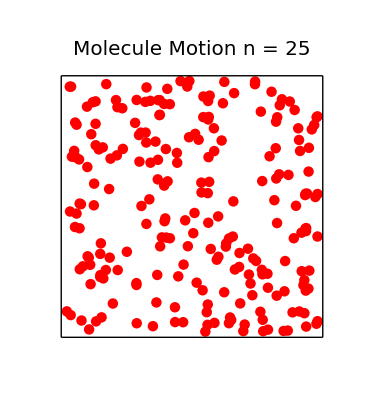

1/20000

51/20000

101/20000

151/20000

201/20000

251/20000

301/20000

351/20000

401/20000

451/20000

501/20000

551/20000

601/20000

651/20000

701/20000

751/20000

801/20000

851/20000

901/20000

951/20000

1001/20000

1051/20000

1101/20000

1151/20000

1201/20000

1251/20000

1301/20000

1351/20000

1401/20000

1451/20000

1501/20000

1551/20000

1601/20000

1651/20000

1701/20000

1751/20000

1801/20000

1851/20000

1901/20000

1951/20000

2001/20000

2051/20000

2101/20000

2151/20000

2201/20000

2251/20000

2301/20000

2351/20000

2401/20000

2451/20000

2501/20000

2551/20000

2601/20000

2651/20000

2701/20000

2751/20000

2801/20000

2851/20000

2901/20000

2951/20000

3001/20000

3051/20000

3101/20000

3151/20000

3201/20000

3251/20000

3301/20000

3351/20000

3401/20000

3451/20000

3501/20000

3551/20000

3601/20000

3651/20000

3701/20000

3751/20000

3801/20000

3851/20000

3901/20000

3951/20000

4001/20000

4051/20000

4101/20000

4151/20000

4201/20000

4251/20000

4301/20000

4351/20000

4401/20000

4451/20000

4501/20000

4551/20000

4601/20000

4651/20000

4701/20000

4751/20000

4801/20000

4851/20000

4901/20000

4951/20000

5001/20000

5051/20000

5101/20000

5151/20000

5201/20000

5251/20000

5301/20000

5351/20000

5401/20000

5451/20000

5501/20000

5551/20000

5601/20000

5651/20000

5701/20000

5751/20000

5801/20000

5851/20000

5901/20000

5951/20000

6001/20000

6051/20000

6101/20000

6151/20000

6201/20000

6251/20000

6301/20000

6351/20000

6401/20000

6451/20000

6501/20000

6551/20000

6601/20000

6651/20000

6701/20000

6751/20000

6801/20000

6851/20000

6901/20000

6951/20000

7001/20000

7051/20000

7101/20000

7151/20000

7201/20000

7251/20000

7301/20000

7351/20000

7401/20000

7451/20000

7501/20000

7551/20000

7601/20000

7651/20000

7701/20000

7751/20000

7801/20000

7851/20000

7901/20000

7951/20000

8001/20000

8051/20000

8101/20000

8151/20000

8201/20000

8251/20000

8301/20000

8351/20000

8401/20000

8451/20000

8501/20000

8551/20000

8601/20000

8651/20000

8701/20000

8751/20000

8801/20000

8851/20000

8901/20000

8951/20000

9001/20000

9051/20000

9101/20000

9151/20000

9201/20000

9251/20000

9301/20000

9351/20000

9401/20000

9451/20000

9501/20000

9551/20000

9601/20000

9651/20000

9701/20000

9751/20000

9801/20000

9851/20000

9901/20000

9951/20000

10001/20000

C:\Users\ChenYangyao\Desktop\pic_ch3_lorenz\mma3d\molecule.gif

```mathematica
temp=Table[{tx[[-1,i]][[1]],ty[[-1,i]][[1]]},{i,1,n}];
g1=Graphics[{Red,Disk[#,r]}]&/@temp;
g2=Graphics[{Black,Thick,Line[#]}]&/@{{{-0.5,-0.5},{-0.5,0.5}},{{0.5,-0.5},{0.5,0.5}},{{-0.5,0.5},{0.5,0.5}},{{-0.5,-0.5},{0.5,-0.5}}};
g3=Graphics[Text[Style["Molecule Motion n = 25",20],{0,0.6}]];
Show[g1,g2,g3,PlotRange->{{-0.6,0.6},{-0.6,0.65}},AspectRatio->Automatic]
```